```mathematica
ClearAll["Global`*"]
```

```mathematica
Data=Import["D:\\sebas\\estudios\\exactas\\materias\\materiasdf\\incertezas\\datos-G9E13.dat","List"];Data=Take[Data,2500];
```

```mathematica
Bins=Table[x,{x,-7,7,0.25}];
```

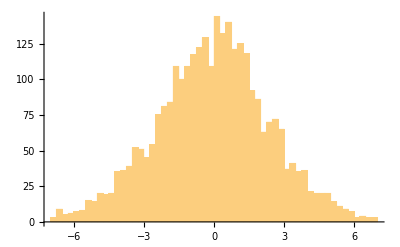

```mathematica
Histogram[Data, Bins]
```

```mathematica
PearsonChiSquareTest[Data,NormalDistribution[0,2.5],"HypothesisTestData"]
```

HypothesisTestData[…]

```mathematica
CramerVonMisesTest[Data,NormalDistribution[0,2.5],"HypothesisTestData"]
```

HypothesisTestData[…]

```mathematica
1/(12 3000)+∑_(i=1)^3000 ((2 i-1)/(2 3000)-CDF[NormalDistribution[0,2.5],Data[[i]]])^2
```

492.312

```mathematica
KolmogorovSmirnovTest[Data,NormalDistribution[0,2.5],"HypothesisTestData"]
```

HypothesisTestData[…]